## Illustrate nonlocal trajectory in simple control system Chapter 4 (controllability in practice)

example adapted from Sun and Motter, PRL 2013

```mathematica
Clear["Global`*"];
SetOptions[{Plot,ParametricPlot},PlotRange -> All,PlotStyle->Thick];
```

```mathematica
a=({{0, 0}, {1, 0}});b=({{1}, {1}});tf=10;ϵ=0.5;
sys=StateSpaceModel[{a,b}];
expA=MatrixExp[a t];vec=Flatten[expA.b];
g=Outer[Times,vec,vec];
P=Integrate[g,{t,0,tf}];
Pinv=Inverse[P];
TraditionalForm /@{vec,expA,g,P,Pinv}
```

{{1,t+1},(1 | 0
t | 1),(1 | t+1
t+1 | (t+1)^2),(10 | 60
60 | 1330/3),(133/250 | -9/125
-9/125 | 3/250)}

```mathematica
x0=({{1}, {0}});xf=({{1}, {-ϵ}}); dx=xf-MatrixExp[a tf].x0;
expA1=MatrixExp[a (tf-t)]ᵀ;
u=bᵀ.expA1.Pinv.dx//Simplify;
TraditionalForm /@{dx,expA1,u}
```

{(0
-10.5),(1 | 10-t
0 | 1),(0.126 t-0.63)}

```mathematica
{x1out,x2out}=OutputResponse[{sys,Flatten[x0]},u[[1,1]],t]
```

{0.+0.063 (15.873-10. t+1. t^2),0.+0.021 (17.619 t-12. t^2+1. t^3)}

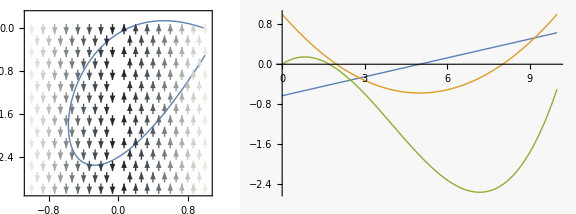

```mathematica
vp=VectorPlot[{0,x},{x,-1,1},{y,.2,-3},VectorColorFunction->"GrayTones"];
pp=ParametricPlot[{x1out,x2out},{t,0,tf}];
pall=Plot[{u,x1out,x2out},{t,0,tf}];
GraphicsRow[{Show[vp,pp],pall},ImageSize->Large]
```

```mathematica
u1=(2u0)/tf1(t-tf1/2)/.u0->6/tf1
```

(12 (t-tf1/2))/tf1^2

```mathematica
{x1out1,x2out1}=OutputResponse[{sys,Flatten[x0]},u1,t]//Simplify
```

{(6 t^2-6 t tf1+tf1^2)/tf1^2,(t (2 t^2-3 t (-2+tf1)+(-6+tf1) tf1))/tf1^2}

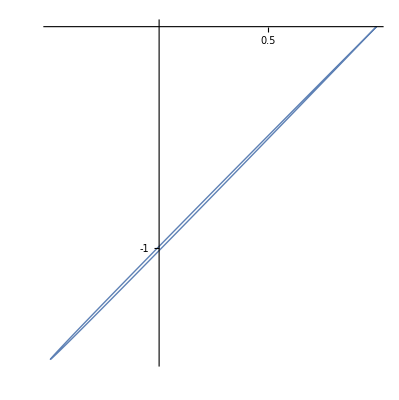

```mathematica
ParametricPlot[{x1out1,x2out1}/.tf1->0.1,{t,0,tf1/.tf1->0.1}]
```

An input u[t] that goes back to itself must cross the x1=0 line, so that it can pick up the required drift “down”.